# Quantities to compute the Primordial Power Spectra written with respect to ΔN:

This can be considered the second notebook of PyPPSinflation.

This script finds the equation needed to obtain the Primordial Power Spectra (PPS) produced by a single-field inflation scenario in the slow-roll approximation, giving a certain model, i.e. a certain potential. 
In order to solve the analytical PPS we start from the model, i.e. the potential, and from this we derive the Hubble Flow Functions (HFFs) ϵ_i written with respect to the number of e-folds ΔN before the end of inflation. The HHFs are the terms which appear in the PPS series functions. 
Because we want all the quantities written with respect to the number of e-folds before the end of inflation, first we need to solve the integral which defines the relation ΔN(ϕ)  and afterwards we need to find ϕ(ΔN) by inverting the result.

The steps are the following:

1) Define the potential, i.e. define the model. As in the general script, we use the KKLT model of inflation.

2) Compute V, V', V'', ϵ_1,  ϵ_2, and  ϵ_3.

3) Compute ϕ_endform the equation ϵ_1(ϕ_end)=1.

4) Compute  ΔN(ϕ) . 

5) Make the inversion of what  obtained in the previous point to find  ϕ(ΔN). 

6) Rewrite all the quantities in terms of ΔN. 

7) Compute the PPS coefficients a or b.

8) Compute the PPS. 

ALERT:
In case the model returns equations that are too difficult to handle, it is possible to simplify the process by computing the analytical PPS using H(N*) and all the  ϵ_i(N_*)values obtained from the numerical PPS. While this approach is not a fully rigorous method for computing the analytical PPS, it has been used in similar cases, such as in Leach et al. (arXiv/0202094).

#### 1) Defining the model

We use the KKLT model of inflation as example:

```mathematica
Mp = 1; 
V0 = V0; 
mp = Sqrt[8 Pi] Mp;
μ = μ; (* mass of the field, e.g. 1.89*10^(-9) Kg*)
(*ϕs= -0.3 Sqrt[8 Pi] Mp   ; an arbitrary value to impose if there is no natural end to inflation*) 
V[ϕ_] := V0 (1+(μ/ϕ ))^(-1); 
dV[ϕ_] := V'[ϕ]; 
ddV[ϕ_] := V'' [ϕ]; 
dddV[ϕ_] := V'''[ϕ];
```

#### 1) Defining the and computing the quantities

Please be aware the epsilon here defined are at leading order LO, as well as H^2 (see the discussion on the 3rd notebook).

```mathematica
Hsq[ϕ_] := 8 Pi V[ϕ]/(3 mp^2);
Subscript[ϵ, 1][ϕ_] := Mp^2/2  (V'[ϕ] /V[ϕ])^2  ;
Subscript[ϵ, 2][ϕ_] := 2 Mp^2(V'[ϕ]^2/V[ϕ]^2-V''[ϕ]/V[ϕ]);
Subscript[ϵ, 3][ϕ_] :=  (2 Mp^4)/(Subscript[ϵ, 2][ϕ])((2 V'[ϕ]^4)/V[ϕ]^4-(3 V'[ϕ]^2 V''[ϕ])/V[ϕ]^3+(V'[ϕ] Derivative[3][V][ϕ])/V[ϕ]^2);
Subscript[ϵ, 4][ϕ_] := (2 Mp^6)/(Subscript[ϵ, 2][ϕ]Subscript[ϵ, 3][ϕ])(+(8 V'[ϕ]^6)/V[ϕ]^6-(17 V'[ϕ]^4 V''[ϕ])/V[ϕ]^5+(6 V'[ϕ]^2 V''[ϕ]^2)/V[ϕ]^4+(5 V'[ϕ]^3 Derivative[3][V][ϕ])/V[ϕ]^4-(V'[ϕ] V''[ϕ] Derivative[3][V][ϕ])/V[ϕ]^3-(V'[ϕ]^2 Derivative[4][V][ϕ])/V[ϕ]^3+(2 Mp^2)/(Subscript[ϵ, 2][ϕ])(-(4 V'[ϕ]^8)/V[ϕ]^8+(12 V'[ϕ]^6 V''[ϕ])/V[ϕ]^7-(9 V'[ϕ]^4 V''[ϕ]^2)/V[ϕ]^6-(4 V'[ϕ]^5 Derivative[3][V][ϕ])/V[ϕ]^6+(6 V'[ϕ]^3 V''[ϕ] Derivative[3][V][ϕ])/V[ϕ]^5-(V'[ϕ]^2 (Derivative[3][V][ϕ])^2)/V[ϕ]^4));
```

```mathematica
FullSimplify[V[ϕ]]
```

(V0 ϕ)/(μ+ϕ)

```mathematica
FullSimplify[dV[ϕ]]
```

(V0 μ)/(μ+ϕ)^2

```mathematica
FullSimplify[ddV[ϕ]]
```

-(2 V0 μ)/(μ+ϕ)^3

```mathematica
FullSimplify[dddV[ϕ]]
```

(6 V0 μ)/(μ+ϕ)^4

```mathematica
FullSimplify[Subscript[ϵ, 1][ϕ]]
```

μ^2/(2 ϕ^2 (μ+ϕ)^2)

```mathematica
FullSimplify[Subscript[ϵ, 2][ϕ]]
```

2/ϕ^2-2/(μ+ϕ)^2

```mathematica
FullSimplify[Subscript[ϵ, 3][ϕ]]
```

(2 μ (μ^2+3 μ ϕ+3 ϕ^2))/(ϕ^2 (μ+ϕ)^2 (μ+2 ϕ))

```mathematica
FullSimplify[Subscript[ϵ, 4][ϕ]]
```

(μ (μ+3 ϕ) (2 μ+3 ϕ) (μ^2+2 μ ϕ+2 ϕ^2))/(ϕ^2 (μ+ϕ)^2 (μ+2 ϕ) (μ^2+3 μ ϕ+3 ϕ^2))

#### 3) Computing ϕ_end from ϵ_1( ϕ_end) = 1

```mathematica
FullSimplify[Solve[ μ^2/(2 ϕ^2 (μ+ϕ)^2)==1, ϕ],Assumptions->μ >0 && ϕe>0 && V0>0 && μ /Mp <<1]
```

{{ϕ→-μ/2-1/2 √(μ (2 √2+μ))},{ϕ→1/2 (-μ+√(μ (2 √2+μ)))},{ϕ→1/2 (-μ-√(μ (-2 √2+μ)))},{ϕ→1/2 (-μ+√(μ (-2 √2+μ)))}}

```mathematica
ϕe[μ_]:= 1/2 (-μ+√(μ (2 √2 +μ)));
```

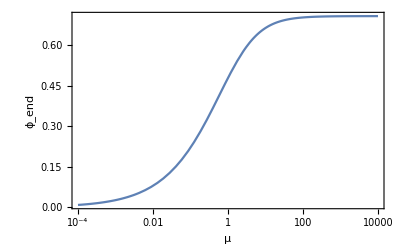

```mathematica
LogLinearPlot[ϕe[μ],{μ,10^-4,10^4},Frame->True,PlotRange->All,FrameLabel->{"μ","ϕ_end"}]
```

#### 3bis) Obtaining ϕ[ΔN] in the case there is no natural end of inflation

In the case there is no natural end of inflation, we are not able to perform the step 3 above.
 We can set the following procedure: choose an arbitrary value for ϕ* and then use N* in the next step to compute ΔN.
 
 We know that 
 ΔN* = N_end - N* = 55  --> N_end =   55+N*
ΔN =N_end - N= -1/Mp^2 (∫_ϕ)^ϕ_end[V[u]/dV[u] du 
Θ=N*-N= -1/Mp^2 (∫_ϕ)^(ϕ*)[V[u]/dV[u] du,
and then we have
ΔN = N_end - N = 55 + N*-N = 55+Θ.

By setting ϕ* we are able to compute Θ.

#### 4+5) Now we put ϕ_end into ΔN, to ϕ[ΔN] by inverting the result

```mathematica
(* In the case there is natural end to inflation and we are able to compute Subscript[ϕ, end] *)
```

```mathematica
FullSimplify[ΔN[ϕ_]:= -1/Mp^2 Integrate[V[u]/dV[u], {u, ϕ,ϕe[μ]}],Assumptions->ΔN>0 && μ >0 && u>0 && V0>0 && ϕ>0]
```

```mathematica
(* In the case there is no natural end to inflation: *)
```

```mathematica
(*FullSimplify[ΔN[ϕ_]:= 55-1/Mp^2 Integrate[V[u]/dV[u], {u, ϕ,ϕs}],Assumptions->V0>0 ]*)
```

```mathematica
FullSimplify[ΔN[ϕ]]
```

-(μ^3+√2 μ √(μ (2 √2+μ))-μ^2 √(μ (2 √2+μ))-6 μ ϕ^2-4 ϕ^3)/(12 μ)

```mathematica
(*Inverting...*) 
f[ϕ_] :=-(μ^3+√2 μ √(μ (2 √2+μ))-μ^2 √(μ (2 √2+μ))-6 μ ϕ^2-4 ϕ^3)/(12 μ);

FullSimplify[InverseFunction[f][ΔN], Assumptions-> ΔN>0&& ϕ>0 && V0>0]
```

1/2 ((12 ΔN μ+(√2-μ) μ √(μ (2 √2+μ))+√2 √(μ^2 ((2 √2-3 μ) μ+12 ΔN (6 ΔN+(√2-μ) √(μ (2 √2+μ))))))^(1/3)+μ (-1+μ/((12 ΔN μ+(√2-μ) μ √(μ (2 √2+μ))+√2 √(μ^2 ((2 √2-3 μ) μ+12 ΔN (6 ΔN+(√2-μ) √(μ (2 √2+μ))))))^(1/3))))

```mathematica
(* Here we check if the function inversion went successfull *)FullSimplify[f[1/2 ((12 ΔN μ+(√2-μ) μ √(μ (2 √2+μ))+√2 √(μ^2 ((2 √2-3 μ) μ+12 ΔN (6 ΔN+(√2-μ) √(μ (2 √2+μ))))))^(1/3)+μ (-1+μ/((12 ΔN μ+(√2-μ) μ √(μ (2 √2+μ))+√2 √(μ^2 ((2 √2-3 μ) μ+12 ΔN (6 ΔN+(√2-μ) √(μ (2 √2+μ))))))^(1/3))))]]
```

ΔN

```mathematica
(* If so, then...*)
```

```mathematica
ϕ[ΔN_]:=1/2 ((12 ΔN μ+(√2-μ) μ √(μ (2 √2+μ))+√2 √(μ^2 ((2 √2-3 μ) μ+12 ΔN (6 ΔN+(√2-μ) √(μ (2 √2+μ))))))^(1/3)+μ (-1+μ/(12 ΔN μ+(√2-μ) μ √(μ (2 √2+μ))+√2 √(μ^2 ((2 √2-3 μ) μ+12 ΔN (6 ΔN+(√2-μ) √(μ (2 √2+μ))))))^(1/3)));
```

#### 6) Rewrite all the quantities in terms of ΔN

```mathematica
Simplify[V[ϕ[ΔN]], Assumptions-> ΔN>0&& ϕ>0 && V0>0]
```

V0/(1+(2 μ)/((12 ΔN μ+(√2-μ) μ √(μ (2 √2+μ))+√2 √(μ^2 ((2 √2-3 μ) μ+12 ΔN (6 ΔN+(√2-μ) √(μ (2 √2+μ))))))^(1/3)+μ (-1+μ/((12 ΔN μ+(√2-μ) μ √(μ (2 √2+μ))+√2 √(μ^2 ((2 √2-3 μ) μ+12 ΔN (6 ΔN+(√2-μ) √(μ (2 √2+μ))))))^(1/3)))))

```mathematica
Simplify[Subscript[ϵ, 1][ϕ[ΔN]], Assumptions-> ΔN>0&& ϕ>0 && V0>0]
```

(8 μ^2)/(((12 ΔN μ+(√2-μ) μ √(μ (2 √2+μ))+√2 √(μ^2 ((2 √2-3 μ) μ+12 ΔN (6 ΔN+(√2-μ) √(μ (2 √2+μ))))))^(1/3)+μ (-1+μ/((12 ΔN μ+(√2-μ) μ √(μ (2 √2+μ))+√2 √(μ^2 ((2 √2-3 μ) μ+12 ΔN (6 ΔN+(√2-μ) √(μ (2 √2+μ))))))^(1/3))))^4 (1+(2 μ)/((12 ΔN μ+(√2-μ) μ √(μ (2 √2+μ))+√2 √(μ^2 ((2 √2-3 μ) μ+12 ΔN (6 ΔN+(√2-μ) √(μ (2 √2+μ))))))^(1/3)+μ (-1+μ/((12 ΔN μ+(√2-μ) μ √(μ (2 √2+μ))+√2 √(μ^2 ((2 √2-3 μ) μ+12 ΔN (6 ΔN+(√2-μ) √(μ (2 √2+μ))))))^(1/3)))))^2)

```mathematica
Simplify[Subscript[ϵ, 2][ϕ[ΔN]], Assumptions-> ΔN>0&& ϕ>0 && V0>0]
```

(32 μ (12 ΔN μ+(√2-μ) μ √(μ (2 √2+μ))+√2 √(μ^2 ((2 √2-3 μ) μ+12 ΔN (6 ΔN+(√2-μ) √(μ (2 √2+μ)))))) (μ^2+(12 ΔN μ+(√2-μ) μ √(μ (2 √2+μ))+√2 √(μ^2 ((2 √2-3 μ) μ+12 ΔN (6 ΔN+(√2-μ) √(μ (2 √2+μ))))))^(2/3)))/((μ^2-μ (12 ΔN μ+(√2-μ) μ √(μ (2 √2+μ))+√2 √(μ^2 ((2 √2-3 μ) μ+12 ΔN (6 ΔN+(√2-μ) √(μ (2 √2+μ))))))^(1/3)+(12 ΔN μ+(√2-μ) μ √(μ (2 √2+μ))+√2 √(μ^2 ((2 √2-3 μ) μ+12 ΔN (6 ΔN+(√2-μ) √(μ (2 √2+μ))))))^(2/3))^2 (μ^2+μ (12 ΔN μ+(√2-μ) μ √(μ (2 √2+μ))+√2 √(μ^2 ((2 √2-3 μ) μ+12 ΔN (6 ΔN+(√2-μ) √(μ (2 √2+μ))))))^(1/3)+(12 ΔN μ+(√2-μ) μ √(μ (2 √2+μ))+√2 √(μ^2 ((2 √2-3 μ) μ+12 ΔN (6 ΔN+(√2-μ) √(μ (2 √2+μ))))))^(2/3))^2)

```mathematica
Simplify[Subscript[ϵ, 3][ϕ[ΔN]], Assumptions-> ΔN>0&& ϕ>0 && V0>0]
```

-((8 μ (-12 ΔN μ-√2 μ √(μ (2 √2+μ))+μ^2 √(μ (2 √2+μ))-√2 √(μ^2 (72 ΔN^2+(2 √2-3 μ) μ+12 ΔN (√2-μ) √(μ (2 √2+μ))))) (3 μ^4+3 μ (12 ΔN+√2 √(μ (2 √2+μ))) (12 ΔN μ+√2 μ √(μ (2 √2+μ))-μ^2 √(μ (2 √2+μ))+√2 √(μ^2 (72 ΔN^2+(2 √2-3 μ) μ+12 ΔN (√2-μ) √(μ (2 √2+μ)))))^(1/3)+3 √2 √(μ^2 (72 ΔN^2+(2 √2-3 μ) μ+12 ΔN (√2-μ) √(μ (2 √2+μ)))) (12 ΔN μ+√2 μ √(μ (2 √2+μ))-μ^2 √(μ (2 √2+μ))+√2 √(μ^2 (72 ΔN^2+(2 √2-3 μ) μ+12 ΔN (√2-μ) √(μ (2 √2+μ)))))^(1/3)-μ^2 (3 √(μ (2 √2+μ)) (12 ΔN μ+√2 μ √(μ (2 √2+μ))-μ^2 √(μ (2 √2+μ))+√2 √(μ^2 (72 ΔN^2+(2 √2-3 μ) μ+12 ΔN (√2-μ) √(μ (2 √2+μ)))))^(1/3)-7 (12 ΔN μ+√2 μ √(μ (2 √2+μ))-μ^2 √(μ (2 √2+μ))+√2 √(μ^2 (72 ΔN^2+(2 √2-3 μ) μ+12 ΔN (√2-μ) √(μ (2 √2+μ)))))^(2/3))))/((μ^2+(12 ΔN μ+(√2-μ) μ √(μ (2 √2+μ))+√2 √(μ^2 ((2 √2-3 μ) μ+12 ΔN (6 ΔN+(√2-μ) √(μ (2 √2+μ))))))^(2/3)) (μ^2-μ (12 ΔN μ+(√2-μ) μ √(μ (2 √2+μ))+√2 √(μ^2 ((2 √2-3 μ) μ+12 ΔN (6 ΔN+(√2-μ) √(μ (2 √2+μ))))))^(1/3)+(12 ΔN μ+(√2-μ) μ √(μ (2 √2+μ))+√2 √(μ^2 ((2 √2-3 μ) μ+12 ΔN (6 ΔN+(√2-μ) √(μ (2 √2+μ))))))^(2/3))^2 (μ^2+μ (12 ΔN μ+(√2-μ) μ √(μ (2 √2+μ))+√2 √(μ^2 ((2 √2-3 μ) μ+12 ΔN (6 ΔN+(√2-μ) √(μ (2 √2+μ))))))^(1/3)+(12 ΔN μ+(√2-μ) μ √(μ (2 √2+μ))+√2 √(μ^2 ((2 √2-3 μ) μ+12 ΔN (6 ΔN+(√2-μ) √(μ (2 √2+μ))))))^(2/3))^2))

```mathematica
Simplify[Subscript[ϵ, 4][ϕ[ΔN]], Assumptions-> ΔN>0&& ϕ>0 && V0>0]
```

-((8 μ^2 (-12 ΔN μ-√2 μ √(μ (2 √2+μ))+μ^2 √(μ (2 √2+μ))-√2 √(μ^2 (72 ΔN^2+(2 √2-3 μ) μ+12 ΔN (√2-μ) √(μ (2 √2+μ))))) (12672 ΔN^2 μ^3+352 √2 μ^4-528 μ^5+53 μ^7+2112 √2 ΔN μ^3 √(μ (2 √2+μ))-2112 ΔN μ^4 √(μ (2 √2+μ))+1056 √2 ΔN μ^2 √(μ^2 (72 ΔN^2+(2 √2-3 μ) μ+12 ΔN (√2-μ) √(μ (2 √2+μ))))+176 μ^2 √(μ (2 √2+μ)) √(μ^2 (72 ΔN^2+(2 √2-3 μ) μ+12 ΔN (√2-μ) √(μ (2 √2+μ))))-88 √2 μ^3 √(μ (2 √2+μ)) √(μ^2 (72 ΔN^2+(2 √2-3 μ) μ+12 ΔN (√2-μ) √(μ (2 √2+μ))))+828 ΔN μ^4 (12 ΔN μ+(√2-μ) μ √(μ (2 √2+μ))+√2 √(μ^2 ((2 √2-3 μ) μ+12 ΔN (6 ΔN+(√2-μ) √(μ (2 √2+μ))))))^(1/3)+69 √2 μ^4 √(μ (2 √2+μ)) (12 ΔN μ+(√2-μ) μ √(μ (2 √2+μ))+√2 √(μ^2 ((2 √2-3 μ) μ+12 ΔN (6 ΔN+(√2-μ) √(μ (2 √2+μ))))))^(1/3)-69 μ^5 √(μ (2 √2+μ)) (12 ΔN μ+(√2-μ) μ √(μ (2 √2+μ))+√2 √(μ^2 ((2 √2-3 μ) μ+12 ΔN (6 ΔN+(√2-μ) √(μ (2 √2+μ))))))^(1/3)+69 √2 μ^3 √(μ^2 (72 ΔN^2+(2 √2-3 μ) μ+12 ΔN (√2-μ) √(μ (2 √2+μ)))) (12 ΔN μ+(√2-μ) μ √(μ (2 √2+μ))+√2 √(μ^2 ((2 √2-3 μ) μ+12 ΔN (6 ΔN+(√2-μ) √(μ (2 √2+μ))))))^(1/3)+2592 ΔN^2 μ (12 ΔN μ+(√2-μ) μ √(μ (2 √2+μ))+√2 √(μ^2 ((2 √2-3 μ) μ+12 ΔN (6 ΔN+(√2-μ) √(μ (2 √2+μ))))))^(2/3)+72 √2 μ^2 (12 ΔN μ+(√2-μ) μ √(μ (2 √2+μ))+√2 √(μ^2 ((2 √2-3 μ) μ+12 ΔN (6 ΔN+(√2-μ) √(μ (2 √2+μ))))))^(2/3)-108 μ^3 (12 ΔN μ+(√2-μ) μ √(μ (2 √2+μ))+√2 √(μ^2 ((2 √2-3 μ) μ+12 ΔN (6 ΔN+(√2-μ) √(μ (2 √2+μ))))))^(2/3)+53 μ^5 (12 ΔN μ+(√2-μ) μ √(μ (2 √2+μ))+√2 √(μ^2 ((2 √2-3 μ) μ+12 ΔN (6 ΔN+(√2-μ) √(μ (2 √2+μ))))))^(2/3)+432 √2 ΔN μ √(μ (2 √2+μ)) (12 ΔN μ+(√2-μ) μ √(μ (2 √2+μ))+√2 √(μ^2 ((2 √2-3 μ) μ+12 ΔN (6 ΔN+(√2-μ) √(μ (2 √2+μ))))))^(2/3)-432 ΔN μ^2 √(μ (2 √2+μ)) (12 ΔN μ+(√2-μ) μ √(μ (2 √2+μ))+√2 √(μ^2 ((2 √2-3 μ) μ+12 ΔN (6 ΔN+(√2-μ) √(μ (2 √2+μ))))))^(2/3)+216 √2 ΔN √(μ^2 (72 ΔN^2+(2 √2-3 μ) μ+12 ΔN (√2-μ) √(μ (2 √2+μ)))) (12 ΔN μ+(√2-μ) μ √(μ (2 √2+μ))+√2 √(μ^2 ((2 √2-3 μ) μ+12 ΔN (6 ΔN+(√2-μ) √(μ (2 √2+μ))))))^(2/3)+36 √(μ (2 √2+μ)) √(μ^2 (72 ΔN^2+(2 √2-3 μ) μ+12 ΔN (√2-μ) √(μ (2 √2+μ)))) (12 ΔN μ+(√2-μ) μ √(μ (2 √2+μ))+√2 √(μ^2 ((2 √2-3 μ) μ+12 ΔN (6 ΔN+(√2-μ) √(μ (2 √2+μ))))))^(2/3)-18 √2 μ √(μ (2 √2+μ)) √(μ^2 (72 ΔN^2+(2 √2-3 μ) μ+12 ΔN (√2-μ) √(μ (2 √2+μ)))) (12 ΔN μ+(√2-μ) μ √(μ (2 √2+μ))+√2 √(μ^2 ((2 √2-3 μ) μ+12 ΔN (6 ΔN+(√2-μ) √(μ (2 √2+μ))))))^(2/3)))/((μ^2+(12 ΔN μ+(√2-μ) μ √(μ (2 √2+μ))+√2 √(μ^2 ((2 √2-3 μ) μ+12 ΔN (6 ΔN+(√2-μ) √(μ (2 √2+μ))))))^(2/3)) (μ^2-μ (12 ΔN μ+(√2-μ) μ √(μ (2 √2+μ))+√2 √(μ^2 ((2 √2-3 μ) μ+12 ΔN (6 ΔN+(√2-μ) √(μ (2 √2+μ))))))^(1/3)+(12 ΔN μ+(√2-μ) μ √(μ (2 √2+μ))+√2 √(μ^2 ((2 √2-3 μ) μ+12 ΔN (6 ΔN+(√2-μ) √(μ (2 √2+μ))))))^(2/3))^2 (μ^2+μ (12 ΔN μ+(√2-μ) μ √(μ (2 √2+μ))+√2 √(μ^2 ((2 √2-3 μ) μ+12 ΔN (6 ΔN+(√2-μ) √(μ (2 √2+μ))))))^(1/3)+(12 ΔN μ+(√2-μ) μ √(μ (2 √2+μ))+√2 √(μ^2 ((2 √2-3 μ) μ+12 ΔN (6 ΔN+(√2-μ) √(μ (2 √2+μ))))))^(2/3))^2 (3 μ^4+3 μ (12 ΔN+√2 √(μ (2 √2+μ))) (12 ΔN μ+√2 μ √(μ (2 √2+μ))-μ^2 √(μ (2 √2+μ))+√2 √(μ^2 (72 ΔN^2+(2 √2-3 μ) μ+12 ΔN (√2-μ) √(μ (2 √2+μ)))))^(1/3)+3 √2 √(μ^2 (72 ΔN^2+(2 √2-3 μ) μ+12 ΔN (√2-μ) √(μ (2 √2+μ)))) (12 ΔN μ+√2 μ √(μ (2 √2+μ))-μ^2 √(μ (2 √2+μ))+√2 √(μ^2 (72 ΔN^2+(2 √2-3 μ) μ+12 ΔN (√2-μ) √(μ (2 √2+μ)))))^(1/3)-μ^2 (3 √(μ (2 √2+μ)) (12 ΔN μ+√2 μ √(μ (2 √2+μ))-μ^2 √(μ (2 √2+μ))+√2 √(μ^2 (72 ΔN^2+(2 √2-3 μ) μ+12 ΔN (√2-μ) √(μ (2 √2+μ)))))^(1/3)-7 (12 ΔN μ+√2 μ √(μ (2 √2+μ))-μ^2 √(μ (2 √2+μ))+√2 √(μ^2 (72 ΔN^2+(2 √2-3 μ) μ+12 ΔN (√2-μ) √(μ (2 √2+μ)))))^(2/3)))))

```mathematica
Simplify[Hsq[ϕ[ΔN]], Assumptions-> ΔN>0&& ϕ>0 && V0>0]
```

V0/(3 (1+(2 μ)/((12 ΔN μ+(√2-μ) μ √(μ (2 √2+μ))+√2 √(μ^2 ((2 √2-3 μ) μ+12 ΔN (6 ΔN+(√2-μ) √(μ (2 √2+μ))))))^(1/3)+μ (-1+μ/((12 ΔN μ+(√2-μ) μ √(μ (2 √2+μ))+√2 √(μ^2 ((2 √2-3 μ) μ+12 ΔN (6 ΔN+(√2-μ) √(μ (2 √2+μ))))))^(1/3))))))

#### Python transformation

To port all these equations in the Python script PyPPSinflation, we need to write them in Python syntax. 
To do so we suggest to use the Mathematica script “ToPython”, written by Gustavo Wiederhecker: https://github.com/gwiederhecker/ToPython.git

```mathematica
Needs["ToPython`"]
```

```mathematica
ToPython[V0/(3 (1+(2 μ)/((12 ΔN μ+(√2-μ) μ √(μ (2 √2+μ))+√2 √(μ^2 ((2 √2-3 μ) μ+12 ΔN (6 ΔN+(√2-μ) √(μ (2 √2+μ))))))^(1/3)+μ (-1+μ/((12 ΔN μ+(√2-μ) μ √(μ (2 √2+μ))+√2 √(μ^2 ((2 √2-3 μ) μ+12 ΔN (6 ΔN+(√2-μ) √(μ (2 √2+μ))))))^(1/3)))))), "np"]
```

1/3 * V0 * ( ( 1 + 2 * mu * ( ( ( ( 12 * DeltaN * mu + ( ( ( 2 )**( 1/2 ) + -1 * mu ) * mu * ( mu * ( 2 * ( 2 )**( 1/2 ) + mu ) )**( 1/2 ) + ( 2 )**( 1/2 ) * ( ( mu )**( 2 ) * ( ( 2 * ( 2 )**( 1/2 ) + -3 * mu ) * mu + 12 * DeltaN * ( 6 * DeltaN + ( ( 2 )**( 1/2 ) + -1 * mu ) * ( mu * ( 2 * ( 2 )**( 1/2 ) + mu ) )**( 1/2 ) ) ) )**( 1/2 ) ) ) )**( 1/3 ) + mu * ( -1 + mu * ( ( 12 * DeltaN * mu + ( ( ( 2 )**( 1/2 ) + -1 * mu ) * mu * ( mu * ( 2 * ( 2 )**( 1/2 ) + mu ) )**( 1/2 ) + ( 2 )**( 1/2 ) * ( ( mu )**( 2 ) * ( ( 2 * ( 2 )**( 1/2 ) + -3 * mu ) * mu + 12 * DeltaN * ( 6 * DeltaN + ( ( 2 )**( 1/2 ) + -1 * mu ) * ( mu * ( 2 * ( 2 )**( 1/2 ) + mu ) )**( 1/2 ) ) ) )**( 1/2 ) ) ) )**( -1/3 ) ) ) )**( -1 ) ) )**( -1 )